12.  Implement a Tag system function which takes a tag rule in the form

```mathematica
{{0,0,x___}->Flatten[{x,replacement00}],{0,1,x___}->Flatten[{x,replacement01}],{1,0,x___}->Flatten[{x,replacement10}],{1,1,x___}->Flatten[{x,replacement11}]}
```

where the replacements are lists of 0's and 1's.  Enumerate rules of this form, make rule icons, and evolution graphics.  Find the first number (under your enumeration) whose Tag system evolution from the simplest initial condition {0,0} which is not essentially cyclic.

```mathematica
filltwo[one_,two_]:= {one,two,x___}->Flatten[{x,#}]& /@ Tuples[{0,1},3]
```

```mathematica
Flatten[filltwo @@@ Tuples[{0,1},2]]
```

{{0,0,x___}→{x,0,0,0},{0,0,x___}→{x,0,0,1},{0,0,x___}→{x,0,1,0},{0,0,x___}→{x,0,1,1},{0,0,x___}→{x,1,0,0},{0,0,x___}→{x,1,0,1},{0,0,x___}→{x,1,1,0},{0,0,x___}→{x,1,1,1},{0,1,x___}→{x,0,0,0},{0,1,x___}→{x,0,0,1},{0,1,x___}→{x,0,1,0},{0,1,x___}→{x,0,1,1},{0,1,x___}→{x,1,0,0},{0,1,x___}→{x,1,0,1},{0,1,x___}→{x,1,1,0},{0,1,x___}→{x,1,1,1},{1,0,x___}→{x,0,0,0},{1,0,x___}→{x,0,0,1},{1,0,x___}→{x,0,1,0},{1,0,x___}→{x,0,1,1},{1,0,x___}→{x,1,0,0},{1,0,x___}→{x,1,0,1},{1,0,x___}→{x,1,1,0},{1,0,x___}→{x,1,1,1},{1,1,x___}→{x,0,0,0},{1,1,x___}→{x,0,0,1},{1,1,x___}→{x,0,1,0},{1,1,x___}→{x,0,1,1},{1,1,x___}→{x,1,0,0},{1,1,x___}→{x,1,0,1},{1,1,x___}→{x,1,1,0},{1,1,x___}→{x,1,1,1}}

```mathematica
(* The number of ways to choose between 8 replacementXX and put them in 4 rules is 8^4 = 4096. There are 4096 possible rules: *)
```

```mathematica
Length[Tuples[filltwo @@@ Tuples[{0,1},2]]]
```

4096

```mathematica
Tuples[filltwo @@@ Tuples[{0,1},2]];
```

```mathematica
(*To enumerate I'll use a number between 0 to 4096-1 written in base 2, with 12 digits. Where digits represent the final state of the evolution *)
```

```mathematica
arg::rulenumber="The rule number should be between 0 and 4096-1";
```

```mathematica
makerule[n_]:=If[n<4096&&n≥0,(Flatten[{#1,x___}]->Flatten[{x,#2}])& @@@ Partition[Riffle[Tuples[{0,1},2],Partition[IntegerDigits[n,2,12],3]],2],Message[arg::rulenumber]]
```

```mathematica
makerule[3281]
```

{{0,0,x___}→{x,1,1,0},{0,1,x___}→{x,0,1,1},{1,0,x___}→{x,0,1,0},{1,1,x___}→{x,0,0,1}}

```mathematica
(* Rule icons: *)
```

```mathematica
printrulecolor[inizio_List,fine_List,colorrule_List]:=Print[LongRightArrow[{Image[ArrayPlot[{inizio},Mesh->True,MeshStyle->Black,ColorRules->colorrule],ImageSize->{Length[inizio]*25,25}],Image[Rasterize["..."]]},{Image[Rasterize["..."]],Image[ArrayPlot[{fine},Mesh->True,MeshStyle->Black,ColorRules->colorrule],ImageSize->{Length[fine]*25,25}]}]]
```

```mathematica
printrulecolor[{0,0},{1,0,1},{1->Black,0->LightGray}]
printrulecolor[{0,1},{1,1,0},{1->Black,0->LightGray}]
printrulecolor[{1,0},{0,1,0},{1->Black,0->LightGray}]
printrulecolor[{1,1},{1,0,0},{1->Black,0->LightGray}]
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-}

«1 more identical outputs»

```mathematica
(* OR *)
```

```mathematica
print[n_,colors_]:=If[n<4096&&n≥0,(printrulecolor[Flatten[#1],Flatten[#2],colors])& @@@Partition[Riffle[Tuples[{0,1},2],Partition[IntegerDigits[n,2,12],3]],2],Message[arg::rulenumber]]
```

```mathematica
(*EVOLUTION*)
```

```mathematica
$colors={1->Black,0->LightGray}
```

{1→GrayLevel[0],0→GrayLevel[0.85]}

```mathematica
evolve[rulenumber_,steps_]:=With[{rule=makerule[rulenumber]},ArrayPlot[NestList[Replace[#,rule] &,{0,0},steps],ColorRules->$colors]]
```

```mathematica
(* From rule number 0 to 511 the output is TRIVIAL, always 0s. *)
```

```mathematica
(* I'll consider something like this (rule 520 or 999) as cyclic. *)
```

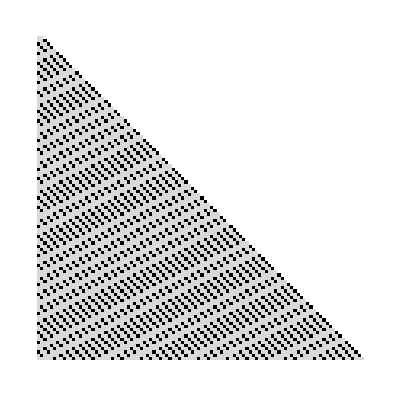
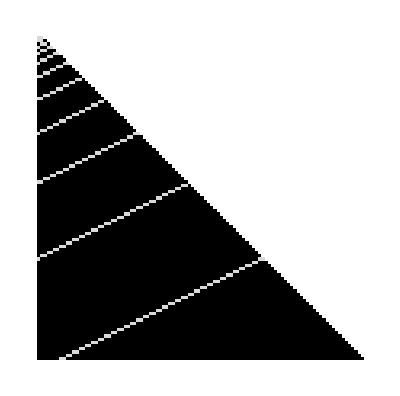

```mathematica
{evolve[520,100],evolve[999,100]}
```

```mathematica
(* This is for instance something random and not cyclic: *)
```

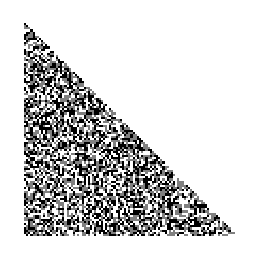

```mathematica
ArrayPlot[Table[RandomInteger[2,i],{i,100}]]
```

```mathematica
(* I've seen the evolution for many rules, we'll see some examples: *)
```

```mathematica
(* I find that the evolution shows regularity in a large number of rules *)
```

```mathematica
evolve[543,1000]
```

-Graphics-

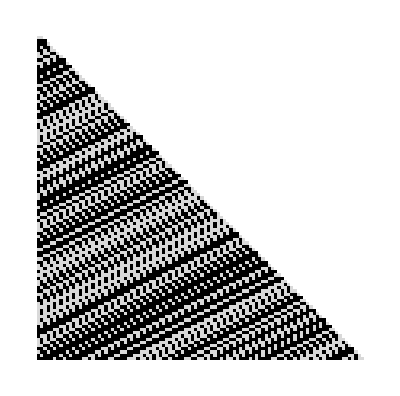
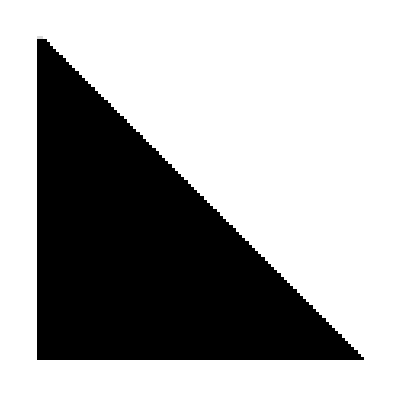
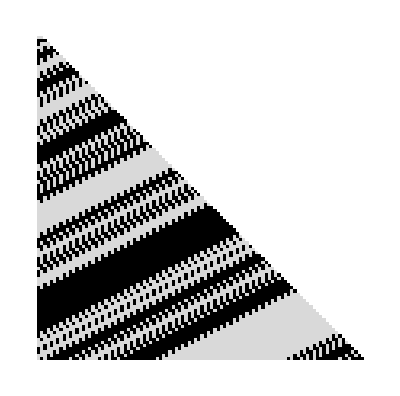
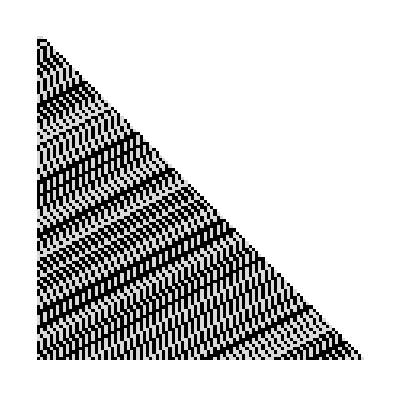
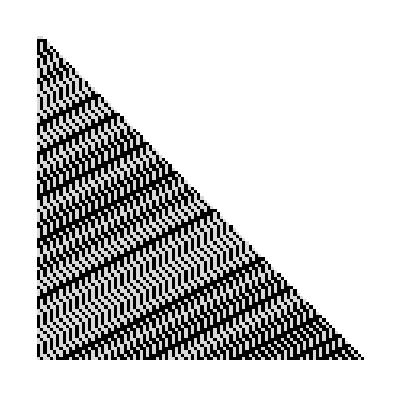
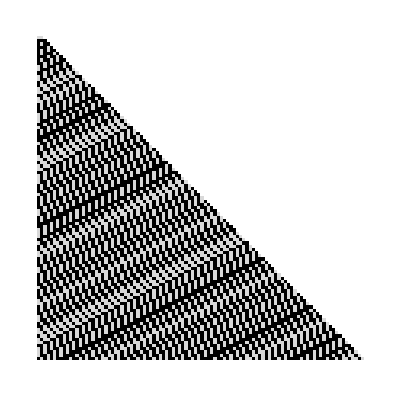
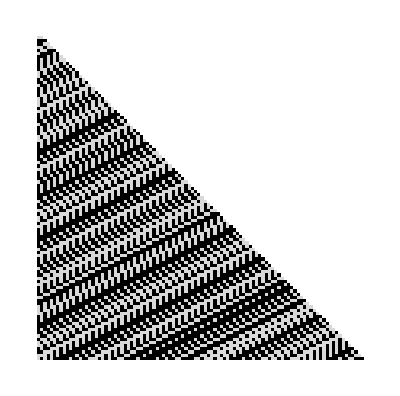
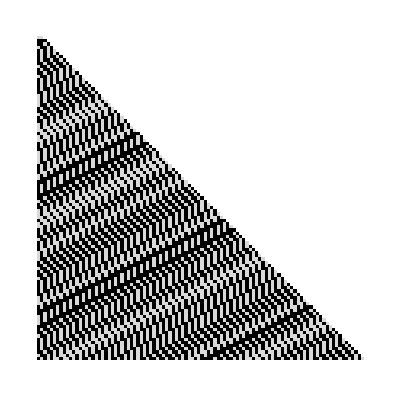
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[evolve[i,100],{i,3750,3770}]
```

```mathematica
{evolve[1255,1000],evolve[1240,1000]}
```

{-Graphics-,-Graphics-}

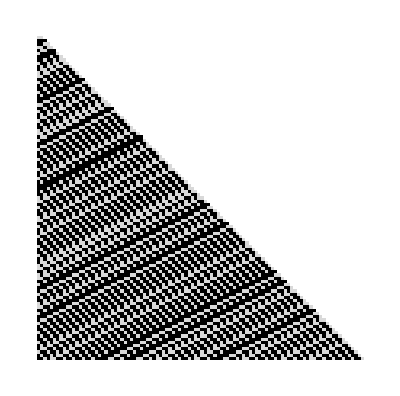
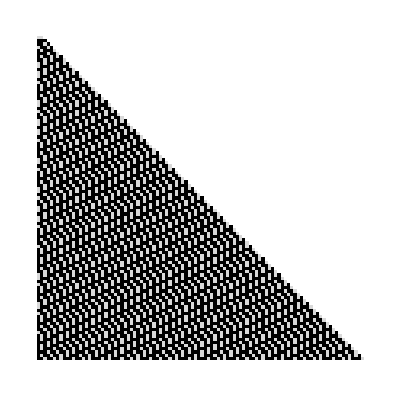
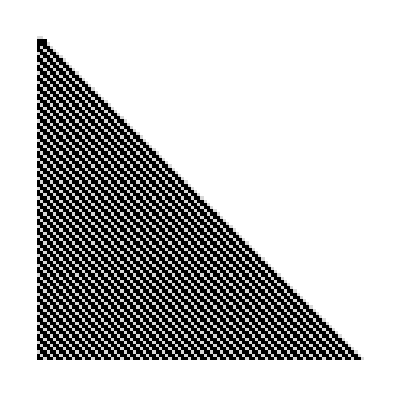
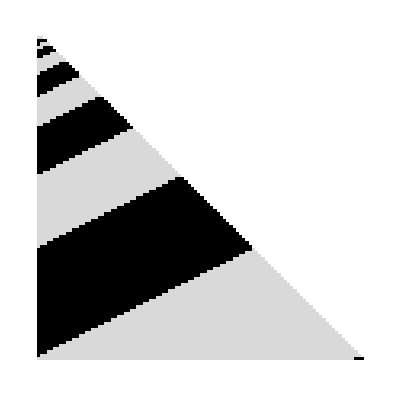
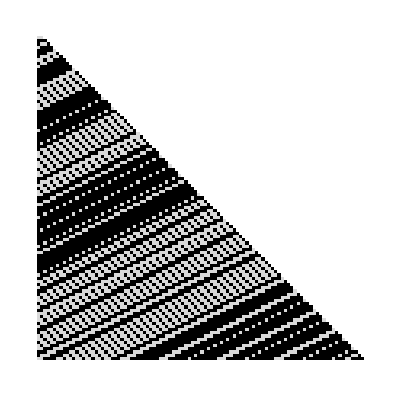
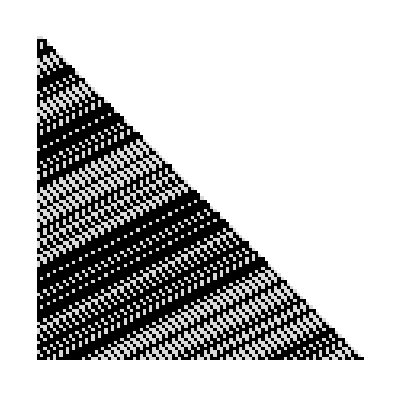
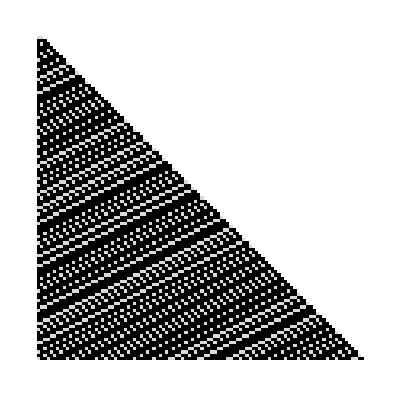
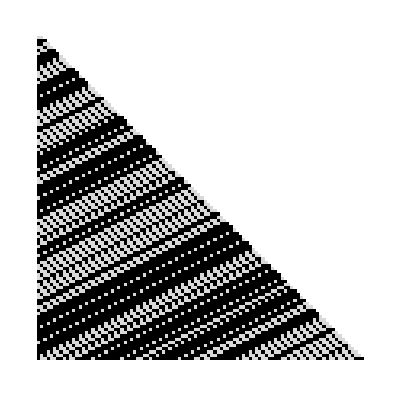
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[evolve[i,100],{i,4020,4040}]
```